```mathematica
v1t=3(UnitStep[t]-2UnitStep[t-1/2000])(UnitStep[t]-UnitStep[t-1/1000]);
v1=LaplaceTransform[v1t,t,s]Sum[Exp[-i s/1000],{i,0,4}];
```

```mathematica
ZC[c_]:=1/(s c);
ZL[l_]:=s l;
fc[c_,l_,r_]:=InverseLaplaceTransform[(v1+3/s)ZC[c]/(ZC[c]+ZL[l]+r)-3/s,s,t];
fl[c_,l_,r_]:=InverseLaplaceTransform[(v1+3/s)ZL[l]/(ZC[c]+ZL[l]+r),s,t];
fr[c_,l_,r_]:=InverseLaplaceTransform[(v1+3/s)r/(ZC[c]+ZL[l]+r),s,t];
f4[c_,l_,r_]:=GraphicsColumn[{
Plot[Evaluate@InverseLaplaceTransform[v1,s,t],{t,1/1000,5/1000},PlotRange->All,AspectRatio->1/6,MaxRecursion->10],
Plot[Evaluate@fc[c,l,r],{t,1/1000,5/1000},PlotRange->All,AspectRatio->1/6,MaxRecursion->10],
Plot[Evaluate@fl[c,l,r],{t,1/1000,5/1000},PlotRange->All,AspectRatio->1/6,MaxRecursion->10],
Plot[Evaluate@fr[c,l,r],{t,1/1000,5/1000},PlotRange->All,AspectRatio->1/6,MaxRecursion->10]
},ImageSize->Large]
```

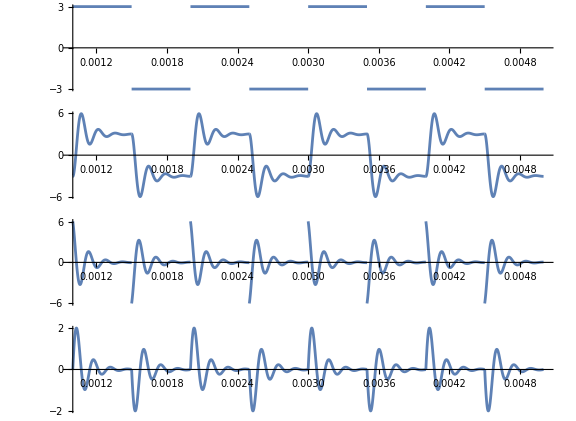

```mathematica
f4[10^-7,5 10^-3,100]
```

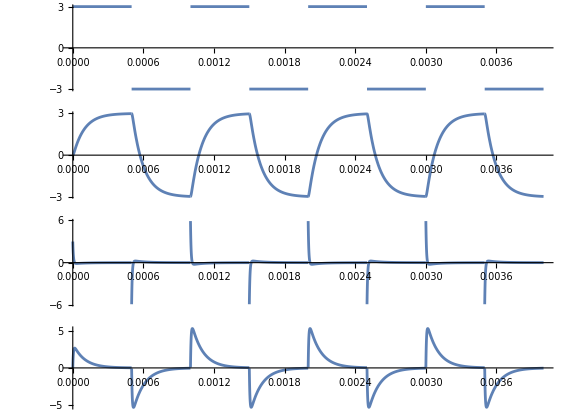

```mathematica
f4[10^-7,5 10^-3,1000]
```

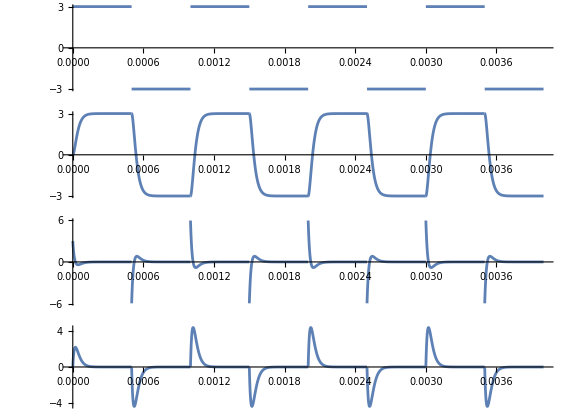

```mathematica
f4[10^-7,5 10^-3,2 √((5 10^-3)/10^-7)]
```

```mathematica
f41[c_,l_,r_]:=Column[{Row[{"C=",N@c," F, L=",N@l," H, R=",N@r," Ω"}],GraphicsColumn[{
Plot[Evaluate@InverseLaplaceTransform[v1,s,t],{t,1/1000,5/1000},PlotRange->All,AspectRatio->1/6,MaxRecursion->10,PlotLabel->"V_s"],
Plot[Evaluate@fc[c,l,r],{t,1/1000,5/1000},PlotRange->All,AspectRatio->1/6,MaxRecursion->10,PlotLabel->"V_C"],
Plot[Evaluate@fl[c,l,r],{t,1/1000,5/1000},PlotRange->All,AspectRatio->1/6,MaxRecursion->10,PlotLabel->"V_L"],
Plot[Evaluate@fr[c,l,r],{t,1/1000,5/1000},PlotRange->All,AspectRatio->1/6,MaxRecursion->10,PlotLabel->"V_R"]
},ImageSize->Large]}]
```

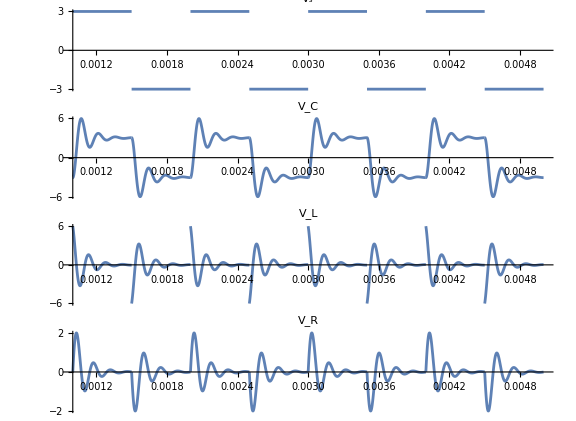
C=1.×10^-7 F, L=0.005 H, R=100. Ω
-Graphics-

```mathematica
f41[10^-7,5 10^-3,100]
```

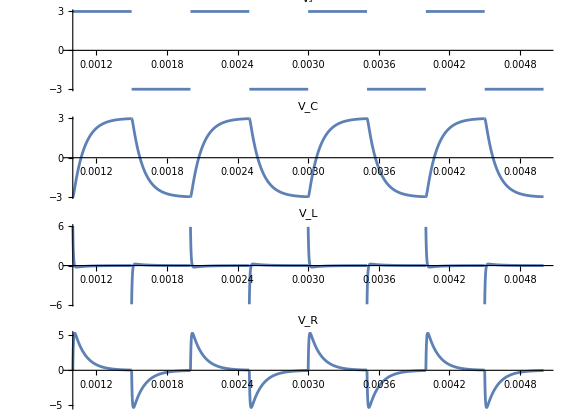
C=1.×10^-7 F, L=0.005 H, R=1000. Ω
-Graphics-

```mathematica
f41[10^-7,5 10^-3,1000]
```

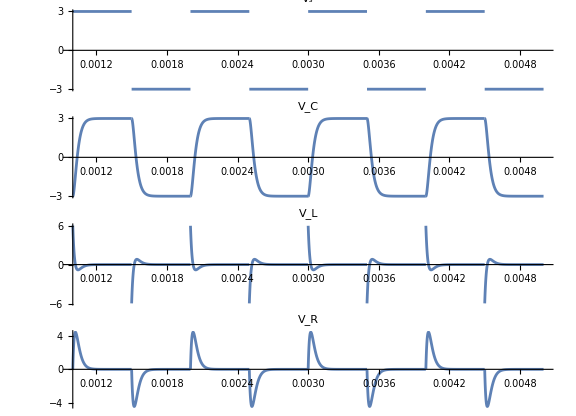
C=1.×10^-7 F, L=0.005 H, R=447.214 Ω
-Graphics-

```mathematica
f41[10^-7,5 10^-3,2 √((5 10^-3)/10^-7)]
```

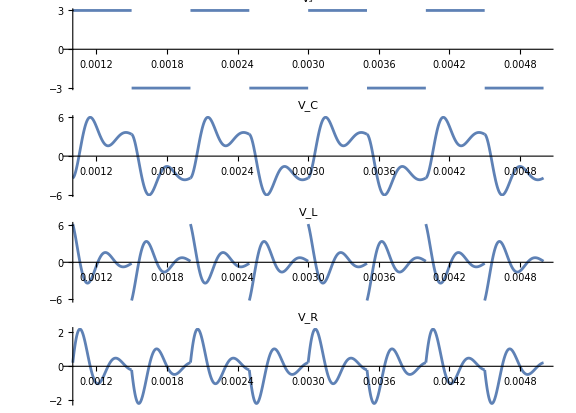
C=2.2×10^-7 F, L=0.01 H, R=100. Ω
-Graphics-

```mathematica
f41[22 10^-8,10 10^-3,100]
```

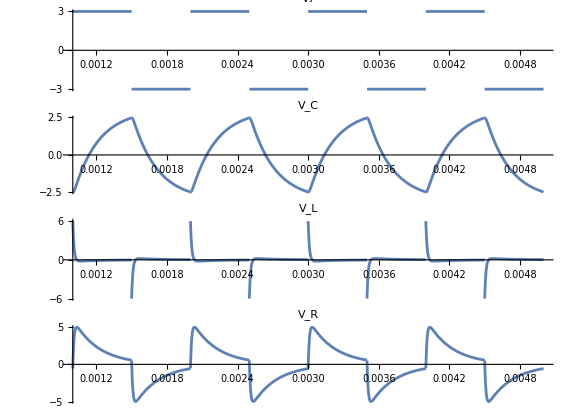
C=2.2×10^-7 F, L=0.01 H, R=1000. Ω
-Graphics-

```mathematica
f41[22 10^-8,10 10^-3,1000]
```

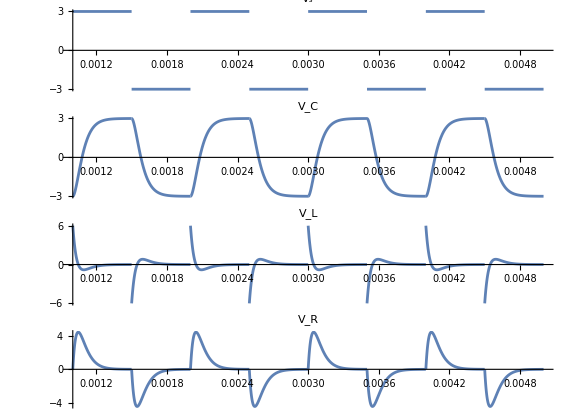
C=2.2×10^-7 F, L=0.01 H, R=426.401 Ω
-Graphics-

```mathematica
f41[22 10^-8,10 10^-3,2 √((10 10^-3)/(22 10^-8))]
```

```mathematica
aaaaa={{Evaluate@fc[10^-7,5 10^-3,100],Evaluate@fc[10^-7,5 10^-3,100]},{Evaluate@fc[10^-7,5 10^-3,100],Evaluate@fc[10^-7,5 10^-3,100]}};
```

```mathematica
plotrule=Sequence[{t,0.0015,0.0035},Frame->True,AxesLabel->None]
```

Sequence[{t,0.0015,0.0035},Frame→True,AxesLabel→None]

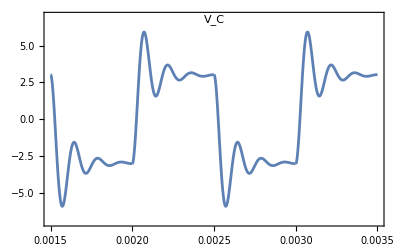

```mathematica
Plot[Evaluate@fc[10^-7,5 10^-3,100],{t,0.0015,0.0035},Frame->True,AxesLabel->None,PlotLegends->Placed["V_C",{Center,Top}],PlotRange->{All,{-7,7}},FrameTicks->{{Automatic,None},None}]
```

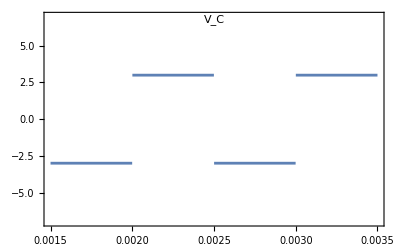

```mathematica
Plot[3SquareWave[1000t],Evaluate@plotrule,FrameTicks->{{Automatic,None},None}]
```

```mathematica
f42[c_,l_,r_,range_]:=GraphicsGrid[{
{Plot[3SquareWave[1000t],Evaluate@plotrule,PlotRange->{All,{-range,range}},FrameTicks->{{{-6,-3,0,3,6},None},{None,None}},PlotLegends->Placed["V_s",{Center,Top}],MaxRecursion->10],
Plot[Evaluate@fc[c,l,r],Evaluate@plotrule,PlotRange->{All,{-range,range}},FrameTicks->{{None,{-6,-3,0,3,6}},{None,None}},PlotLegends->Placed["V_C",{Center,Top}],MaxRecursion->10]},

{Plot[Evaluate@fl[c,l,r],Evaluate@plotrule,PlotRange->{All,{-range,range}},FrameTicks->{{{-6,-3,0,3,6},None},{None,None}},PlotLegends->Placed["V_L",{Center,Top}],MaxRecursion->10],
Plot[Evaluate@fr[c,l,r],Evaluate@plotrule,PlotRange->{All,{-range,range}},FrameTicks->{{None,{-6,-3,0,3,6}},{None,None}},PlotLegends->Placed["V_R",{Center,Top}],MaxRecursion->10]}
},ImageSize->Large,Spacings->Scaled[0.04]]
```

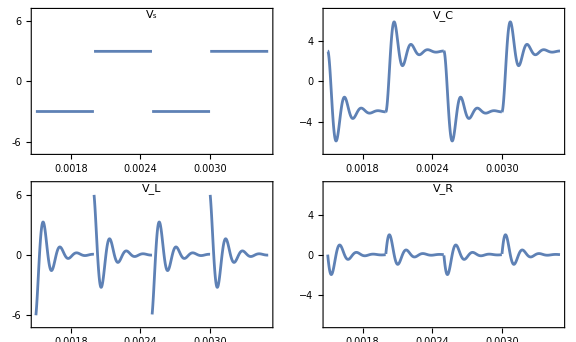

```mathematica
f42[10^-7,5 10^-3,100,7]
```

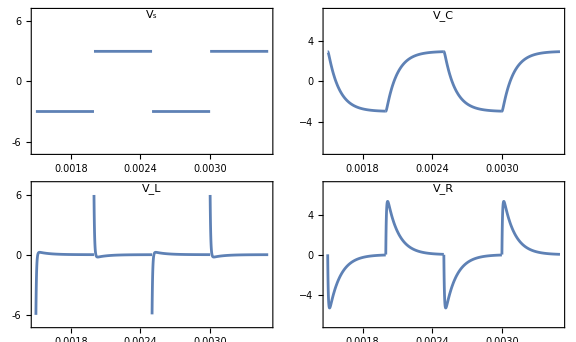

```mathematica
f42[10^-7,5 10^-3,1000,7]
```

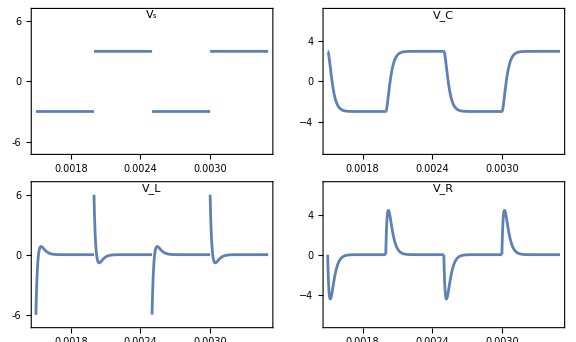

```mathematica
f42[10^-7,5 10^-3,2 √((5 10^-3)/10^-7),7]
```